```mathematica
ClearAll["Global`*"]
```

# Coupled Qutrit-Qubit Quantum Thermal Diode

In this paper, we propose a quantum thermal diode model based on a coupled qutrit - qubit system to regulate the heat flow between two thermal baths. This numerical simulations show the diode characteristics of our model.  We acknowledge the use of modules and functions of supplementary materials of Ref[31].

#### Pauli Matrices for Two-Level-System (Qubit)

```mathematica
Subscript[σ, x] = ({{0, 1}, {1, 0}}) ;
Subscript[σ, y] = ({{0, -ⅈ}, {ⅈ, 0}});
Subscript[σ, z] = ({{1, 0}, {0, -1}});
Subscript[σ, I] = ({{1, 0}, {0, 1}});
SubPlus[σ] = MatrixForm[1/2*(Subscript[σ, x] + ⅈ*Subscript[σ, y])];
SubMinus[σ] =MatrixForm[1/2*(Subscript[σ, x] - ⅈ*Subscript[σ, y])];
```

There are two energy states in a qubit and they can be described by two column vectors.

```mathematica
Subscript[z, 0]=Transpose[{{0,1}}];
Subscript[z, 1]=Transpose[{{1,0}}];
```

#### Pauli Matrix Equivalents for Three-Level-System (Qutrit)

```mathematica
Subscript[Σ, x] = ({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) ;
Subscript[Σ, y] = ({{0, -i, 0}, {i, 0, -i}, {0, i, 0}});
Subscript[Σ, z] =({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Subscript[Σ, I] = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

There are three energy states in a qutrit and they can be described by three column vectors .

```mathematica
Subscript[Z, 0]=Transpose[{{0,0,1}}];
Subscript[Z, 1]=Transpose[{{0,1,0}}];
Subscript[Z, 2]=Transpose[{{1,0,0}}];
```

#### Qubit Hamiltonian ( assuming ground state energy is 0 and excited state energy is E_3 )

```mathematica
Subscript[H, Two]=Subscript[𝔼, 3]* Subscript[z, 1].Subscript[z, 1] ᵀ;
MatrixForm[%]
```

(𝔼_3 | 0
0 | 0)

#### Qutrit Hamiltonian ( assuming ground state energy is 0 and excited states energies are E_1 and E_2 )

```mathematica
Subscript[H, Three]=Subscript[𝔼, 1]* Subscript[Z, 1].Subscript[Z, 1] ᵀ + Subscript[𝔼, 2]* Subscript[Z, 2].Subscript[Z, 2] ᵀ;
MatrixForm[%]
```

(𝔼_2 | 0 | 0
0 | 𝔼_1 | 0
0 | 0 | 0)

#### Free Hamiltonian of the system

```mathematica
Subscript[H, 0]=KroneckerProduct[Subscript[H, Three],Subscript[σ, I]]+KroneckerProduct[Subscript[Σ, I],Subscript[H, Two]];
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | 𝔼_2 | 0 | 0 | 0 | 0
0 | 0 | 𝔼_1+𝔼_3 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### Free Hamiltonian Eigenvalues and Eigenstates

```mathematica
Eigensystem[Subscript[H, 0]]//MatrixForm
```

(0 | 𝔼_1 | 𝔼_2 | 𝔼_3 | 𝔼_1+𝔼_3 | 𝔼_2+𝔼_3
{0,0,0,0,0,1} | {0,0,0,1,0,0} | {0,1,0,0,0,0} | {0,0,0,0,1,0} | {0,0,1,0,0,0} | {1,0,0,0,0,0})

We can obtain the same eigenstates by taking the tensor product between individual system states.

```mathematica
Subscript[S, i_,j_]:=KroneckerProduct[Subscript[Z, i],Subscript[z, j]]
```

```mathematica
Subscript[S, 2,1]
Subscript[S, 2,0]
Subscript[S, 1,1]
Subscript[S, 1,0]
Subscript[S, 0,1]
Subscript[S, 0,0]
```

{{1},{0},{0},{0},{0},{0}}

{{0},{1},{0},{0},{0},{0}}

{{0},{0},{1},{0},{0},{0}}

{{0},{0},{0},{1},{0},{0}}

{{0},{0},{0},{0},{1},{0}}

{{0},{0},{0},{0},{0},{1}}

To enable transitions between different states without an input of external energy,we take E_2=E_1+ E_3 (resonance condition). With this condition we now have two degenerate energy eigenstates |11⟩  and |20⟩, which can be swapped without an input from external sources.

|11⟩ State: S_(1,1)

```mathematica
Subscript[S, 1,1]
```

{{0},{0},{1},{0},{0},{0}}

| 20⟩ State: S_(2,0)

```mathematica
Subscript[S, 2,0]
```

{{0},{1},{0},{0},{0},{0}}

Write |11⟩  and |20⟩ states as column vectors:

```mathematica
Subscript[S, 11]=Transpose[{{0,0,1,0,0,0}}];
Subscript[S, 20]=Transpose[{{0,1,0,0,0,0}}];
```

#### Interaction Hamiltonian between qubit and qutrit

For transitions between |11⟩  and |20⟩ , we introduce an interaction Hamiltonian. g is the interaction energy between the qutrit and qubit.

```mathematica
Subscript[H, int]=g *( KroneckerProduct[Subscript[S, 11],Subscript[S, 20] ᵀ]+KroneckerProduct[Subscript[S, 20],Subscript[S, 11] ᵀ]);
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | g | 0 | 0 | 0
0 | g | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### Total System Hamiltonian

```mathematica
Subscript[H, s]=Subscript[H, 0]+Subscript[H, int]/.{Subscript[𝔼, 1]+Subscript[𝔼, 3]->Subscript[𝔼, 2]};
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | 𝔼_2 | g | 0 | 0 | 0
0 | g | 𝔼_2 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

As total system Hamiltonian is not diagonalized, we should 1st find it's eigenvalues and eigenvectors in order to find the invertible matrix A ( here the unitary transformation) which creates a diagonalized system Hamiltonian.

```mathematica
{Φ,v}=Eigensystem[Subscript[H, s]]
```

{{0,𝔼_1,-g+𝔼_2,g+𝔼_2,𝔼_3,𝔼_2+𝔼_3},{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,-1,1,0,0,0},{0,1,1,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}}

```mathematica
Norm/@v
```

{1,1,√2,√2,1,1}

#### Eigenstates as the tensor product of individual states

Normalized Eigenstates in matrix form

```mathematica
Subscript[λ, 1]=Transpose[{{1,0,0,0,0,0}}];
Flatten[KroneckerProduct[Subscript[Z, 2],Subscript[z, 1]]]
```

{1,0,0,0,0,0}

```mathematica
Subscript[λ, 2]=Transpose[{{0,1/(√2),1/(√2),0,0,0}}];
Flatten[1/(√2)*(KroneckerProduct[Subscript[Z, 1],Subscript[z, 1]]+KroneckerProduct[Subscript[Z, 2],Subscript[z, 0]])]
```

{0,1/(√2),1/(√2),0,0,0}

```mathematica
Subscript[λ, 3]=Transpose[{{0,-1/(√2),1/(√2),0,0,0}}];
Flatten[1/(√2)*(KroneckerProduct[Subscript[Z, 1],Subscript[z, 1]]-KroneckerProduct[Subscript[Z, 2],Subscript[z, 0]])]
```

{0,-1/(√2),1/(√2),0,0,0}

```mathematica
Subscript[λ, 4]=Transpose[{{0,0,0,1,0,0}}];
Flatten[KroneckerProduct[Subscript[Z, 1],Subscript[z, 0]]]
```

{0,0,0,1,0,0}

```mathematica
Subscript[λ, 5]=Transpose[{{0,0,0,0,1,0}}];
Flatten[KroneckerProduct[Subscript[Z, 0],Subscript[z, 1]]]
```

{0,0,0,0,1,0}

```mathematica
Subscript[λ, 6]=Transpose[{{0,0,0,0,0,1}}];
Flatten[KroneckerProduct[Subscript[Z, 0],Subscript[z, 0]]]
```

{0,0,0,0,0,1}

Matrix A can be formed by having these basis vectors (eigenstates)  as columns.
A=(1 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | -1/(√2) | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
A={{1,0,0,0,0,0},{0,1/(√2),-1/(√2),0,0,0},{0,1/(√2),1/(√2),0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
```

Then, the diagonalized total system Hamiltonian is,

```mathematica
Subscript[H, sys]=Simplify[Inverse[A].Subscript[H, s].A];
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | g+𝔼_2 | 0 | 0 | 0 | 0
0 | 0 | -g+𝔼_2 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[Eigensystem[Subscript[H, sys]]]
```

{{0,𝔼_1,-g+𝔼_2,g+𝔼_2,𝔼_3,𝔼_2+𝔼_3},{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}}

Eigenvalues of the total system Hamiltonian in matrix form

```mathematica
HsEVal ={Subscript[𝔼, 2]+Subscript[𝔼, 3],g+Subscript[𝔼, 2],-g+Subscript[𝔼, 2],Subscript[𝔼, 1],Subscript[𝔼, 3],0}//MatrixForm;
```

## Quantum Master Equation

#### Density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, i,j][t],{i,1,6},{j,1,6}];
MatrixForm[%]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t])

#### Possible Transition Frequencies

```mathematica
ωMatrix={Flatten[Table[Subscript[ω, i,j],{i,1,6},{j,i+1,6}]]}
```

{{ω_(1,2),ω_(1,3),ω_(1,4),ω_(1,5),ω_(1,6),ω_(2,3),ω_(2,4),ω_(2,5),ω_(2,6),ω_(3,4),ω_(3,5),ω_(3,6),ω_(4,5),ω_(4,6),ω_(5,6)}}

```mathematica
ωVals=Flatten[Simplify[Table[(HsEVal[[1,i]]-HsEVal[[1,j]])/ℏ,{i,1,6},{j,i+1,6}]]]/.{Subscript[𝔼, 1]+Subscript[𝔼, 3]->Subscript[𝔼, 2]}
```

{(-g+𝔼_3)/ℏ,(g+𝔼_3)/ℏ,(-𝔼_1+𝔼_2+𝔼_3)/ℏ,𝔼_2/ℏ,(𝔼_2+𝔼_3)/ℏ,(2 g)/ℏ,(g-𝔼_1+𝔼_2)/ℏ,(g+𝔼_2-𝔼_3)/ℏ,(g+𝔼_2)/ℏ,-(g+𝔼_1-𝔼_2)/ℏ,-(g-𝔼_2+𝔼_3)/ℏ,(-g+𝔼_2)/ℏ,(𝔼_1-𝔼_3)/ℏ,𝔼_1/ℏ,𝔼_3/ℏ}

#### Projection Operators

```mathematica
Subscript[πMatrix, i_] := Subscript[λ, i].Subscript[λ, i] ᵀ
```

#### Lindblad Operator

```mathematica
Subscript[σ, x L]=KroneckerProduct[Subscript[Σ, x],Subscript[σ, I]];
Subscript[σ, x R]=KroneckerProduct[Subscript[Σ, I],Subscript[σ, x]];
```

```mathematica
Subscript[AMatrix, P_,Subscript[ω, j_,i_]]:= Subscript[πMatrix, i].Subscript[σ, x P].Subscript[πMatrix, j]
```

```mathematica
Table[MatrixForm[Subscript[AMatrix, L,Subscript[ω, j,i]]],{j,1,6},{i,j+1,6}]
```

{{(0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{}}

```mathematica
Table[MatrixForm[Subscript[AMatrix, R,Subscript[ω, j,i]]],{j,1,6},{i,j+1,6}]
```

{{(0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)},{}}

#### Lindblad Super Operator

```mathematica
Subscript[ℒ, P_]:=Subscript[ℒ, P]=∑_(α=1)^15 (Subscript[𝒥, P][Part[ωMatrix,1,α]](1+Subscript[n, P][Part[ωMatrix,1,α]])(Subscript[AMatrix, P,Part[ωMatrix,1,α]].ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,α]].ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,α]])+(Subscript[𝒥, P][Part[ωMatrix,1,α]] Subscript[n, P][Part[ωMatrix,1,α]](Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]]-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,α]].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ)));
```

#### Master Equation

```mathematica
dρ=MatrixForm[Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, sys].ρMatrix[t]-ρMatrix[t].Subscript[H, sys]))]//.{-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, P,j,i],Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, P,j,i]};
```

```mathematica
MatrixForm[%]
```

Density Matrix Diagonal Elements

We have used results from section Simulation : Solutions using NDSolve to made the assumptions ρ_(2,2)=ρ_(3,3) and   ρ_(2,3)→ 0,ρ_(3,2)→ 0 to simplify the following expressions.

(ρ̇)_(1,1)

```mathematica
Simplify[Simplify[dρ[[1,1]][[1]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{Subscript[n, P_][Subscript[ω, j_,2]]Subscript[𝒥, P_][Subscript[ω, j_,2]](Subscript[ρ, 2,2][t]+Subscript[ρ, k_,k_][t]):>2 Subscript[n, P][Subscript[ω, j,2]]Subscript[𝒥, P][Subscript[ω, j,2]]Subscript[ρ, 2,2][t],Subscript[n, P_][Subscript[ω, j_,3]]Subscript[𝒥, P_][Subscript[ω, j_,3]](Subscript[ρ, k_,k_][t]+Subscript[ρ, 3,3][t]):>2 Subscript[n, P][Subscript[ω, j,3]]Subscript[𝒥, P][Subscript[ω, j,3]]Subscript[ρ, 3,3][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

1/2 (-((1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)] ρ_(1,1)[t])-(1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t]-(1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]-(1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)] ρ_(1,1)[t]+n_L[ω_(1,2)] 𝒥_L[ω_(1,2)] ρ_(2,2)[t]+n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]+n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t]+n_R[ω_(1,3)] 𝒥_R[ω_(1,3)] ρ_(3,3)[t])

(ρ̇)_(2,2)

```mathematica
Subscript[ρ̇, 2,2]=Simplify[Simplify[dρ[[1,2]][[2]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{-Subscript[n, P_][Subscript[ω, j_,3]]Subscript[𝒥, P_][Subscript[ω, j_,3]]Subscript[ρ, 2,2][t]:>-Subscript[n, P][Subscript[ω, j,3]]Subscript[𝒥, P][Subscript[ω, j,3]]Subscript[ρ, 3,3][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]])Subscript[𝒥, P_][Subscript[ω, 3,i_]]Subscript[ρ, 2,2][t]:>(1+Subscript[n, P][Subscript[ω, 3,i]])Subscript[𝒥, P][Subscript[ω, 3,i]]Subscript[ρ, 3,3][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

1/4 (Γ_(L,1,2)+Γ_(L,1,3)+Γ_(R,1,2)+Γ_(R,1,3)-(1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]-(1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)] ρ_(2,2)[t]-(1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)] ρ_(2,2)[t]-(1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)] ρ_(3,3)[t]-(1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]-(1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]+n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]+n_L[ω_(3,4)] 𝒥_L[ω_(3,4)] ρ_(4,4)[t]+n_R[ω_(2,4)] 𝒥_R[ω_(2,4)] ρ_(4,4)[t]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t]+n_L[ω_(2,5)] 𝒥_L[ω_(2,5)] ρ_(5,5)[t]+n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t])

(ρ̇)_(3,3)

```mathematica
Subscript[ρ̇, 3,3]=Simplify[Simplify[dρ[[1,3]][[3]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{-Subscript[n, P_][Subscript[ω, j_,2]] Subscript[𝒥, P_][Subscript[ω, j_,2]] Subscript[ρ, 3,3][t]:>-Subscript[n, P][Subscript[ω, j,2]] Subscript[𝒥, P][Subscript[ω, j,2]] Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 2,i_]]) Subscript[𝒥, P_][Subscript[ω, 2,i_]] Subscript[ρ, 3,3][t]:>(1+Subscript[n, P][Subscript[ω, 2,i]]) Subscript[𝒥, P][Subscript[ω, 2,i]] Subscript[ρ, 2,2][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

1/4 (Γ_(L,1,2)+Γ_(L,1,3)+Γ_(R,1,2)+Γ_(R,1,3)-(1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]-(1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)] ρ_(2,2)[t]-(1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)] ρ_(2,2)[t]-(1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)] ρ_(3,3)[t]-(1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]-(1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]+n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]+n_L[ω_(3,4)] 𝒥_L[ω_(3,4)] ρ_(4,4)[t]+n_R[ω_(2,4)] 𝒥_R[ω_(2,4)] ρ_(4,4)[t]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t]+n_L[ω_(2,5)] 𝒥_L[ω_(2,5)] ρ_(5,5)[t]+n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t])

```mathematica
Subscript[ρ̇, 2,2]==Subscript[ρ̇, 3,3]
```

True

(ρ̇)_(4,4)

```mathematica
Simplify[Simplify[dρ[[1,4]][[4]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{(1+Subscript[n, P_][Subscript[ω, 2,i_]])Subscript[𝒥, P_][Subscript[ω, 2,i_]](Subscript[ρ, 2,2][t]+Subscript[ρ, k_,k_][t]):>2 (1+Subscript[n, P][Subscript[ω, 2,i]])Subscript[𝒥, P][Subscript[ω, 2,i]]Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]])Subscript[𝒥, P_][Subscript[ω, 3,i_]](Subscript[ρ, k_,k_][t]+Subscript[ρ, 3,3][t]):>2(1+Subscript[n, P][Subscript[ω, 3,i]])Subscript[𝒥, P][Subscript[ω, 3,i]]Subscript[ρ, 3,3][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

1/2 (Γ_(L,2,4)+Γ_(L,3,4)-2 Γ_(L,4,6)+Γ_(R,2,4)+Γ_(R,3,4))

(ρ̇)_(5,5)

```mathematica
Simplify[Simplify[dρ[[1,5]][[5]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{(1+Subscript[n, P_][Subscript[ω, 2,i_]])Subscript[𝒥, P_][Subscript[ω, 2,i_]](Subscript[ρ, 2,2][t]+Subscript[ρ, k_,k_][t]):>2 (1+Subscript[n, P][Subscript[ω, 2,i]])Subscript[𝒥, P][Subscript[ω, 2,i]]Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]])Subscript[𝒥, P_][Subscript[ω, 3,i_]](Subscript[ρ, k_,k_][t]+Subscript[ρ, 3,3][t]):>2(1+Subscript[n, P][Subscript[ω, 3,i]])Subscript[𝒥, P][Subscript[ω, 3,i]]Subscript[ρ, 3,3][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

1/2 (-2 Γ_(R,5,6)+𝒥_L[ω_(2,5)] ((1+n_L[ω_(2,5)]) ρ_(2,2)[t]-n_L[ω_(2,5)] ρ_(5,5)[t])+𝒥_L[ω_(3,5)] ((1+n_L[ω_(3,5)]) ρ_(3,3)[t]-n_L[ω_(3,5)] ρ_(5,5)[t]))

(ρ̇)_(6,6)

```mathematica
Simplify[Simplify[dρ[[1,6]][[6]]/.{ Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}]/.{Subscript[n, P_][Subscript[ω, j_,2]]Subscript[𝒥, P_][Subscript[ω, j_,2]](Subscript[ρ, 2,2][t]+Subscript[ρ, k_,k_][t]):>2 Subscript[n, P][Subscript[ω, j,2]]Subscript[𝒥, P][Subscript[ω, j,2]]Subscript[ρ, 2,2][t],Subscript[n, P_][Subscript[ω, j_,3]]Subscript[𝒥, P_][Subscript[ω, j_,3]](Subscript[ρ, k_,k_][t]+Subscript[ρ, 3,3][t]):>2 Subscript[n, P][Subscript[ω, j,3]]Subscript[𝒥, P][Subscript[ω, j,3]]Subscript[ρ, 3,3][t]}]//.{(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t]:>Subscript[Γ, P,j,i],-(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]+Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] :>-Subscript[Γ, P,j,i]}
```

Γ_(L,4,6)+Γ_(R,5,6)

#### Thermal Energy Flows

```mathematica
HsMatrix=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6]}]
```

{{ℏ ω_1,0,0,0,0,0},{0,ℏ ω_2,0,0,0,0},{0,0,ℏ ω_3,0,0,0},{0,0,0,ℏ ω_4,0,0},{0,0,0,0,ℏ ω_5,0},{0,0,0,0,0,ℏ ω_6}}

```mathematica
Subscript[J, P_]:=Subscript[J, P]=Tr[Subscript[ℒ, P].HsMatrix]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]};
```

```mathematica
Subscript[J, L]//.{Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}//.{Subscript[n, P_][Subscript[ω, j_,2]] Subscript[𝒥, P_][Subscript[ω, j_,2]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 Subscript[n, P][Subscript[ω, j,2]] Subscript[𝒥, P][Subscript[ω, j,2]] Subscript[ρ, 2,2][t],Subscript[n, P_][Subscript[ω, j_,3]] Subscript[𝒥, P_][Subscript[ω, j_,3]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 Subscript[n, P][Subscript[ω, j,3]] Subscript[𝒥, P][Subscript[ω, j,3]] Subscript[ρ, 3,3][t],(1+Subscript[n, P_][Subscript[ω, 2,i_]])Subscript[𝒥, P_][Subscript[ω, 2,i_]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 (1+Subscript[n, P][Subscript[ω, 2,i]])Subscript[𝒥, P][Subscript[ω, 2,i]] Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]])Subscript[𝒥, P_][Subscript[ω, 3,i_]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 (1+Subscript[n, P][Subscript[ω, 3,i]])Subscript[𝒥, P][Subscript[ω, 3,i]] Subscript[ρ, 3,3][t], Subscript[n, P_][Subscript[ω, j_,3]] Subscript[𝒥, P_][Subscript[ω, j_,3]] Subscript[ρ, 2,2][t]:> Subscript[n, P][Subscript[ω, j,3]] Subscript[𝒥, P][Subscript[ω, j,3]] Subscript[ρ, 3,3][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]]) Subscript[𝒥, P_][Subscript[ω, 3,i_]] Subscript[ρ, 2,2][t]:>(1+Subscript[n, P][Subscript[ω, 3,i]]) Subscript[𝒥, P][Subscript[ω, 3,i]] Subscript[ρ, 3,3][t]}//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]}
```

ℏ ω_6 Γ_(L,4,6)+ℏ ω_1 (-1/2 (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)] ρ_(1,1)[t]-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t]+1/2 n_L[ω_(1,2)] 𝒥_L[ω_(1,2)] ρ_(2,2)[t]+1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t])+ℏ ω_4 (-Γ_(L,4,6)+1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]+1/2 (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)] ρ_(3,3)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]-1/2 n_L[ω_(3,4)] 𝒥_L[ω_(3,4)] ρ_(4,4)[t])+ℏ ω_5 (1/2 (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)] ρ_(2,2)[t]+1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]-1/2 n_L[ω_(2,5)] 𝒥_L[ω_(2,5)] ρ_(5,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t])+ℏ ω_2 (1/4 (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)] ρ_(1,1)[t]+1/4 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t]-1/4 n_L[ω_(1,2)] 𝒥_L[ω_(1,2)] ρ_(2,2)[t]-1/4 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]-1/4 (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)] ρ_(2,2)[t]-1/4 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]+1/4 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]+1/4 n_L[ω_(3,4)] 𝒥_L[ω_(3,4)] ρ_(4,4)[t]+1/4 n_L[ω_(2,5)] 𝒥_L[ω_(2,5)] ρ_(5,5)[t]+1/4 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t])+ℏ ω_3 (1/4 (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)] ρ_(1,1)[t]+1/4 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t]-1/4 n_L[ω_(1,2)] 𝒥_L[ω_(1,2)] ρ_(3,3)[t]-1/4 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)] ρ_(3,3)[t]-1/4 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]+1/4 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]+1/4 n_L[ω_(3,4)] 𝒥_L[ω_(3,4)] ρ_(4,4)[t]+1/4 n_L[ω_(2,5)] 𝒥_L[ω_(2,5)] ρ_(5,5)[t]+1/4 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t])

```mathematica
Subscript[J, R]//.{Subscript[ρ, 2,3][t]-> 0,Subscript[ρ, 3,2][t]-> 0}//.{Subscript[n, P_][Subscript[ω, j_,2]] Subscript[𝒥, P_][Subscript[ω, j_,2]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 Subscript[n, P][Subscript[ω, j,2]] Subscript[𝒥, P][Subscript[ω, j,2]] Subscript[ρ, 2,2][t],Subscript[n, P_][Subscript[ω, j_,3]] Subscript[𝒥, P_][Subscript[ω, j_,3]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 Subscript[n, P][Subscript[ω, j,3]] Subscript[𝒥, P][Subscript[ω, j,3]] Subscript[ρ, 3,3][t],(1+Subscript[n, P_][Subscript[ω, 2,i_]])Subscript[𝒥, P_][Subscript[ω, 2,i_]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 (1+Subscript[n, P][Subscript[ω, 2,i]])Subscript[𝒥, P][Subscript[ω, 2,i]] Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]])Subscript[𝒥, P_][Subscript[ω, 3,i_]] (1/4 Subscript[ρ, 2,2][t]+1/4 Subscript[ρ, 3,3][t]):>1/2 (1+Subscript[n, P][Subscript[ω, 3,i]])Subscript[𝒥, P][Subscript[ω, 3,i]] Subscript[ρ, 3,3][t], Subscript[n, P_][Subscript[ω, j_,3]] Subscript[𝒥, P_][Subscript[ω, j_,3]] Subscript[ρ, 2,2][t]:> Subscript[n, P][Subscript[ω, j,3]] Subscript[𝒥, P][Subscript[ω, j,3]] Subscript[ρ, 3,3][t],(1+Subscript[n, P_][Subscript[ω, 3,i_]]) Subscript[𝒥, P_][Subscript[ω, 3,i_]] Subscript[ρ, 2,2][t]:>(1+Subscript[n, P][Subscript[ω, 3,i]]) Subscript[𝒥, P][Subscript[ω, 3,i]] Subscript[ρ, 3,3][t],Subscript[n, P_][Subscript[ω, j_,2]] Subscript[𝒥, P_][Subscript[ω, j_,2]] Subscript[ρ, 3,3][t]:> Subscript[n, P][Subscript[ω, j,2]] Subscript[𝒥, P][Subscript[ω, j,2]] Subscript[ρ, 2,2][t],(1+Subscript[n, P_][Subscript[ω, 2,i_]]) Subscript[𝒥, P_][Subscript[ω, 2,i_]] Subscript[ρ, 3,3][t]:>(1+Subscript[n, P][Subscript[ω, 2,i]]) Subscript[𝒥, P][Subscript[ω, 2,i]] Subscript[ρ, 2,2][t]}//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]}
```

-ℏ ω_5 Γ_(R,5,6)+ℏ ω_6 Γ_(R,5,6)+ℏ ω_1 (-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]-1/2 (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)] ρ_(1,1)[t]+1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]+1/2 n_R[ω_(1,3)] 𝒥_R[ω_(1,3)] ρ_(3,3)[t])+ℏ ω_4 (1/2 (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)] ρ_(2,2)[t]+1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]-1/2 n_R[ω_(2,4)] 𝒥_R[ω_(2,4)] ρ_(4,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t])+ℏ ω_2 (1/4 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]+1/4 (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)] ρ_(1,1)[t]-1/4 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]-1/4 (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)] ρ_(2,2)[t]-1/4 n_R[ω_(1,3)] 𝒥_R[ω_(1,3)] ρ_(3,3)[t]-1/4 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]+1/4 n_R[ω_(2,4)] 𝒥_R[ω_(2,4)] ρ_(4,4)[t]+1/4 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t])+ℏ ω_3 (1/4 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]+1/4 (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)] ρ_(1,1)[t]-1/4 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]-1/4 (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)] ρ_(2,2)[t]-1/4 n_R[ω_(1,3)] 𝒥_R[ω_(1,3)] ρ_(3,3)[t]-1/4 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]+1/4 n_R[ω_(2,4)] 𝒥_R[ω_(2,4)] ρ_(4,4)[t]+1/4 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t])

## Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

#### Stationary State Solutions of master equation

```mathematica
RHS=Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, sys].ρMatrix[t]-ρMatrix[t].Subscript[H, sys]));
```

```mathematica
MatrixForm[%]
```

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t])

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,6},{j,1,6}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;7]];
soloffdiag=Delete[sol,Table[{1+7i},{i,0,5}]];
```

Off diagonal Solutions

```mathematica
Flatten[{soloffdiag/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]}}];
soloffdiagstat=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, i,j]-i,j Subscript[ρ, i,j],{i,1,6},{j,1,6}]],0]]
```

{{ρ_(1,2)→0,ρ_(1,3)→0,ρ_(1,4)→0,ρ_(1,5)→0,ρ_(1,6)→0,ρ_(2,1)→0,ρ_(2,3)→-((1/8 ρ_(2,2) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/8 ρ_(3,3) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]-1/4 ρ_(1,1) (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)]-1/8 ρ_(2,2) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]-1/8 ρ_(3,3) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]+1/4 ρ_(1,1) (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)]-1/4 ρ_(4,4) n_L[ω_(2,4)] 𝒥_L[ω_(2,4)]+1/8 ρ_(2,2) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/8 ρ_(3,3) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]-1/4 ρ_(5,5) n_L[ω_(2,5)] 𝒥_L[ω_(2,5)]+1/8 ρ_(2,2) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/8 ρ_(3,3) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/4 ρ_(4,4) n_L[ω_(3,4)] 𝒥_L[ω_(3,4)]-1/8 ρ_(2,2) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]-1/8 ρ_(3,3) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]+1/4 ρ_(5,5) n_L[ω_(3,5)] 𝒥_L[ω_(3,5)]-1/8 ρ_(2,2) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]-1/8 ρ_(3,3) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]+1/8 ρ_(2,2) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/8 ρ_(3,3) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]-1/4 ρ_(1,1) (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)]-1/8 ρ_(2,2) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]-1/8 ρ_(3,3) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]+1/4 ρ_(1,1) (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)]-1/4 ρ_(4,4) n_R[ω_(2,4)] 𝒥_R[ω_(2,4)]+1/8 ρ_(2,2) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/8 ρ_(3,3) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/4 ρ_(4,4) n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]-1/8 ρ_(2,2) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)]-1/8 ρ_(3,3) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)])/((2 ⅈ g)/ℏ+1/4 n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/4 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]+1/4 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/4 (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/4 (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]+1/4 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]+1/4 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/4 n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]+1/4 (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/4 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)])),ρ_(2,4)→0,ρ_(2,5)→0,ρ_(2,6)→0,ρ_(3,1)→0,ρ_(3,2)→-((1/8 ρ_(2,2) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/8 ρ_(3,3) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]-1/4 ρ_(1,1) (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)]-1/8 ρ_(2,2) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]-1/8 ρ_(3,3) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]+1/4 ρ_(1,1) (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)]-1/4 ρ_(4,4) n_L[ω_(2,4)] 𝒥_L[ω_(2,4)]+1/8 ρ_(2,2) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/8 ρ_(3,3) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]-1/4 ρ_(5,5) n_L[ω_(2,5)] 𝒥_L[ω_(2,5)]+1/8 ρ_(2,2) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/8 ρ_(3,3) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/4 ρ_(4,4) n_L[ω_(3,4)] 𝒥_L[ω_(3,4)]-1/8 ρ_(2,2) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]-1/8 ρ_(3,3) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]+1/4 ρ_(5,5) n_L[ω_(3,5)] 𝒥_L[ω_(3,5)]-1/8 ρ_(2,2) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]-1/8 ρ_(3,3) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]+1/8 ρ_(2,2) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/8 ρ_(3,3) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]-1/4 ρ_(1,1) (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)]-1/8 ρ_(2,2) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]-1/8 ρ_(3,3) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]+1/4 ρ_(1,1) (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)]-1/4 ρ_(4,4) n_R[ω_(2,4)] 𝒥_R[ω_(2,4)]+1/8 ρ_(2,2) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/8 ρ_(3,3) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/4 ρ_(4,4) n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]-1/8 ρ_(2,2) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)]-1/8 ρ_(3,3) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)])/(-(2 ⅈ g)/ℏ+1/4 n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/4 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]+1/4 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/4 (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]+1/4 (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]+1/4 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]+1/4 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/4 n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]+1/4 (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]+1/4 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)])),ρ_(3,4)→0,ρ_(3,5)→0,ρ_(3,6)→0,ρ_(4,1)→0,ρ_(4,2)→0,ρ_(4,3)→0,ρ_(4,5)→0,ρ_(4,6)→0,ρ_(5,1)→0,ρ_(5,2)→0,ρ_(5,3)→0,ρ_(5,4)→0,ρ_(5,6)→0,ρ_(6,1)→0,ρ_(6,2)→0,ρ_(6,3)→0,ρ_(6,4)→0,ρ_(6,5)→0}}

```mathematica
Flatten[{soloffdiag/.Subscript[ρ, i_,j_][t]-> i,j Subscript[ρ, i,j]}]
```

{ρ_(1,2)'[t]==0,ρ_(1,3)'[t]==0,ρ_(1,4)'[t]==0,ρ_(1,5)'[t]==0,ρ_(1,6)'[t]==0,ρ_(2,1)'[t]==0,ρ_(2,3)'[t]==-1/8 (ρ_(2,2)+ρ_(3,3)) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/4 ρ_(1,1) (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)]+1/8 (ρ_(2,2)+ρ_(3,3)) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]-1/4 ρ_(1,1) (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)]+1/4 ρ_(4,4) n_L[ω_(2,4)] 𝒥_L[ω_(2,4)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/4 ρ_(5,5) n_L[ω_(2,5)] 𝒥_L[ω_(2,5)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]-1/4 ρ_(4,4) n_L[ω_(3,4)] 𝒥_L[ω_(3,4)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]-1/4 ρ_(5,5) n_L[ω_(3,5)] 𝒥_L[ω_(3,5)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]-1/8 (ρ_(2,2)+ρ_(3,3)) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/4 ρ_(1,1) (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)]+1/8 (ρ_(2,2)+ρ_(3,3)) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]-1/4 ρ_(1,1) (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)]+1/4 ρ_(4,4) n_R[ω_(2,4)] 𝒥_R[ω_(2,4)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]-1/4 ρ_(4,4) n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)],ρ_(2,4)'[t]==0,ρ_(2,5)'[t]==0,ρ_(2,6)'[t]==0,ρ_(3,1)'[t]==0,ρ_(3,2)'[t]==-1/8 (ρ_(2,2)+ρ_(3,3)) n_L[ω_(1,2)] 𝒥_L[ω_(1,2)]+1/4 ρ_(1,1) (1+n_L[ω_(1,2)]) 𝒥_L[ω_(1,2)]+1/8 (ρ_(2,2)+ρ_(3,3)) n_L[ω_(1,3)] 𝒥_L[ω_(1,3)]-1/4 ρ_(1,1) (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)]+1/4 ρ_(4,4) n_L[ω_(2,4)] 𝒥_L[ω_(2,4)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)]+1/4 ρ_(5,5) n_L[ω_(2,5)] 𝒥_L[ω_(2,5)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(2,5)]) 𝒥_L[ω_(2,5)]-1/4 ρ_(4,4) n_L[ω_(3,4)] 𝒥_L[ω_(3,4)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(3,4)]) 𝒥_L[ω_(3,4)]-1/4 ρ_(5,5) n_L[ω_(3,5)] 𝒥_L[ω_(3,5)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)]-1/8 (ρ_(2,2)+ρ_(3,3)) n_R[ω_(1,2)] 𝒥_R[ω_(1,2)]+1/4 ρ_(1,1) (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)]+1/8 (ρ_(2,2)+ρ_(3,3)) n_R[ω_(1,3)] 𝒥_R[ω_(1,3)]-1/4 ρ_(1,1) (1+n_R[ω_(1,3)]) 𝒥_R[ω_(1,3)]+1/4 ρ_(4,4) n_R[ω_(2,4)] 𝒥_R[ω_(2,4)]-1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_R[ω_(2,4)]) 𝒥_R[ω_(2,4)]-1/4 ρ_(4,4) n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+1/8 (ρ_(2,2)+ρ_(3,3)) (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)],ρ_(3,4)'[t]==0,ρ_(3,5)'[t]==0,ρ_(3,6)'[t]==0,ρ_(4,1)'[t]==0,ρ_(4,2)'[t]==0,ρ_(4,3)'[t]==0,ρ_(4,5)'[t]==0,ρ_(4,6)'[t]==0,ρ_(5,1)'[t]==0,ρ_(5,2)'[t]==0,ρ_(5,3)'[t]==0,ρ_(5,4)'[t]==0,ρ_(5,6)'[t]==0,ρ_(6,1)'[t]==0,ρ_(6,2)'[t]==0,ρ_(6,3)'[t]==0,ρ_(6,4)'[t]==0,ρ_(6,5)'[t]==0}

As our system states |2⟩ and |3⟩ are degenerate when the internal interaction g << , the population densities ρ_(2,2)=ρ_(3,3) and as shown in the below simulations, ρ_(2,3)=0 and ρ_(3,2)=0 . Therefore, although ρ_(2,3) and ρ_(3,2) states seems to be non-zero in steady state according to above results, they will also decay to zero in steady state.

Diagonal Solutions using NDSolve

Assumptions for the calculations

```mathematica
ωassum1=Flatten[{Table[Subscript[ω, i,j]->(HsEVal[[1,i]]-HsEVal[[1,j]] )/ℏ,{i,1,6},{j,1,6}]}];
ωassum2={Table[Subscript[ω, i]-> HsEVal[[1,i]]/ℏ,{i,1,6}]};
(*unitassum = {k-> 1,ℏ->1};*)
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.300/0.2;
Econv=Tconv k/.unitassum;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τimeconv=(Tconv k)/ℏ/.unitassum;
Jconv=ℏ/Econv^2 /.unitassum;
Jassum1=Subscript[𝒥, p_][ω_]->κ ω;
Jassum=𝒥[ω_]->κ ω;
tmax=(2100/ωconv)/.unitassum;
```

Energy scale of the system (Δ)

```mathematica
Econv
```

2.0709×10^-23

Forward Condition

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.95Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.05 Econv,g->0.01Econv,κ-> 1 };
dynamicsF1=NDSolve[Flatten[{sol//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}],Table[Subscript[ρ, i,j][0]==i,j i,6 1,{i,1,6},{j,1,6}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
```

Reverse Condition

```mathematica
TassumR={Subscript[T, L]-> 0.02 Tconv,Subscript[T, R]-> 0.2 Tconv,Subscript[𝔼, 1]->0.95Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.05 Econv,g->0.01Econv,κ-> 1 };
dynamicsR1=NDSolve[Flatten[{sol//.Flatten[{Jassum1,Jassum,NBEassum,TassumR,unitassum,ωassum1}],Table[Subscript[ρ, i,j][0]==i,j i,6 1,{i,1,6},{j,1,6}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
```

#### Density Matrix Element Plots

Forward Condition:

Density  matrix  diagonals

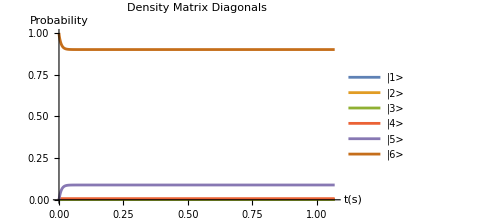

```mathematica
D1=Flatten[{Table[Subscript[ρ, i,i][t],{i,1,6}]}/.dynamicsF1];
P1=Plot[D1,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

Density  matrix  off -diagonals: this confirms that all off-diagonals decay to zero.

```mathematica
D1=Flatten[{{Subscript[ρ, 2,3][t],Subscript[ρ, 3,2][t]}}/.dynamicsF1];
P1=Plot[D1,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

-Graphics-

Reverse Condition:

Density   matrix   diagonals

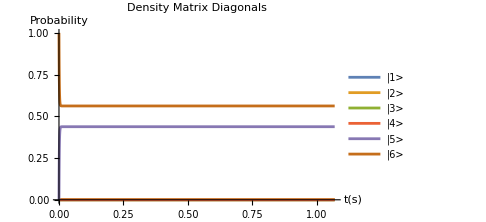

```mathematica
Flatten[{Table[Subscript[ρ, i,i][t],{i,1,6}]}/.dynamicsR1];
P1=Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

Density  matrix  off -diagonals

```mathematica
D1=Flatten[{{Subscript[ρ, 2,3][t],Subscript[ρ, 3,2][t]}}/.dynamicsR1];
P1=Plot[D1,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

-Graphics-

#### Transition Rates

```mathematica
Subscript[Γ, P_,j_,i_]=-Subscript[ρ, i,i][t] Subscript[𝒥, P][Subscript[ω, j,i]]Subscript[n, P][Subscript[ω, j,i]]+Subscript[ρ, j,j][t]Subscript[𝒥, P][Subscript[ω, j,i]](1+Subscript[n, P][Subscript[ω, j,i]]);
```

Forward Condition

```mathematica
Flatten[{Subscript[Γ, L,1,3],Subscript[Γ, L,1,2],Subscript[Γ, L,2,4],Subscript[Γ, L,3,4]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}]/.dynamicsF1];
```

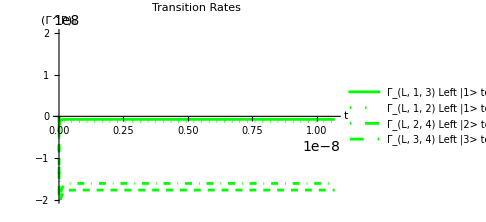

```mathematica
Plot[%,{t,0,tmax},PlotRange-> {-2×10^8,2×10^8},AxesStyle->Directive[Darker[Gray]],ImageSize->Medium,PlotLabel-> Style["Transition Rates"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Γ_(L, 1, 3)  Left |1> to |3>","Γ_(L, 1, 2)  Left |1> to |2>","Γ_(L, 2, 4)  Left |2> to |4>","Γ_(L, 3, 4)  Left |3> to |4>"},PlotStyle->{{Green},{Green,Dotted},{Green,DotDashed},{Green,Dashed}},ImageSize->Large]
```

```mathematica
Flatten[{Subscript[Γ, L,3,5],Subscript[Γ, L,2,5],Subscript[Γ, L,4,6]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}]/.dynamicsF1];
```

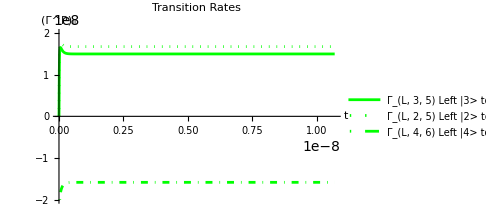

```mathematica
Plot[%,{t,0,tmax},PlotRange-> {-2×10^8,2×10^8},AxesStyle->Directive[Darker[Gray]],ImageSize->Medium,PlotLabel-> Style["Transition Rates"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Γ_(L, 3, 5)  Left |3> to |5>","Γ_(L, 2, 5)  Left |2> to |5>","Γ_(L, 4, 6)  Left |4> to |6>"},PlotStyle->{{Green},{Green,Dotted},{Green,DotDashed}},ImageSize->Large]
```

```mathematica
Flatten[{Subscript[Γ, R,1,2],Subscript[Γ, R,1,3],Subscript[Γ, R,2,4],Subscript[Γ, R,3,4],Subscript[Γ, R,5,6]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}]/.dynamicsF1];
```

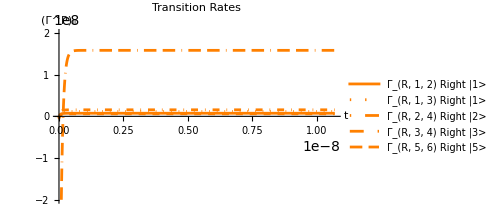

```mathematica
Plot[%,{t,0,tmax},PlotRange-> {-2×10^8,2×10^8},AxesStyle->Directive[Darker[Gray]],ImageSize->Medium,PlotLabel-> Style["Transition Rates"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Γ_(R, 1, 2)  Right |1> to |2>","Γ_(R, 1, 3)  Right |1> to |3>","Γ_(R, 2, 4)  Right |2> to |4>","Γ_(R, 3, 4)  Right |3> to |4>","Γ_(R, 5, 6)  Right |5> to |6>"},PlotStyle->{{Orange},{Orange,Dotted},{Orange,DotDashed},{Orange,Dashed},{Orange,Dashing[{0.025,0.025/2,0.025,0.025/2,0.001,0.025/2}]}},ImageSize->Large]
```

#### Energy Flows

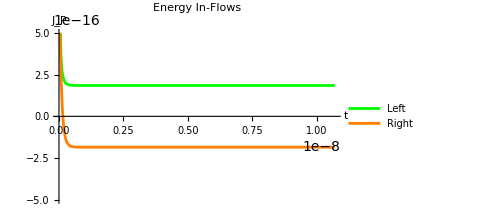

```mathematica
Flatten[{Subscript[J, L],Subscript[J, R]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1,ωassum2}]/.dynamicsF1];
Plot[%,{t,0,tmax},PlotRange-> {-5×10^-16,5×10^-16},ImageSize->Medium,AxesLabel->{"t","J_P"},PlotLabel-> Style["Energy In-Flows"],PlotLegends->{"Left ","Right"},PlotStyle->{Green,Orange}]
```

#### Steady State Solutions for density matrices, transition rates and energy flows

```mathematica
varFunc[TL_,TR_,E1s_,E2s_,E3s_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum1,Jassum,ωassum1,ωassum2,NBEassum,unitassum,κ->1,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[𝔼, 1]->E1s,Subscript[𝔼, 2]->E2s,Subscript[𝔼, 3]->E3s,g->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^6 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]]]]];
Re[{Flatten[Table[Subscript[ρ, i,i],{i,1,6}]/.temp3],Flatten[{Subscript[Γ, L,1,3],Subscript[Γ, L,1,2],Subscript[Γ, L,2,4],Subscript[Γ, L,3,4],Subscript[Γ, L,3,5],Subscript[Γ, L,2,5],Subscript[Γ, L,4,6],Subscript[Γ, R,1,2],Subscript[Γ, R,1,3],Subscript[Γ, R,2,4],Subscript[Γ, R,3,4],Subscript[Γ, R,5,6]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],Flatten[{Subscript[J, L],Subscript[J, R]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]}]]
```

```mathematica
varFunc[0.2 Tconv,0.02 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum]
varFunc[0.02 Tconv,0.2 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum]
```

{{0.001034,0.00160916,0.00160916,0.00694716,0.088673,0.900127},{-7.18679×10^6,-1.22832×10^7,-1.60807×10^8,-1.76737×10^8,1.49519×10^8,1.67156×10^8,-1.58158×10^8,7.41471×10^6,1.18277×10^7,1.5664×10^7,6.07699×10^6,1.58158×10^8},{1.84851×10^-16,-1.84851×10^-16}}

{{7.00412×10^-22,1.10104×10^-21,1.10104×10^-21,1.3784×10^-21,0.437823,0.562177},{8.005×10^-12,5.00901×10^-12,1.28014×10^-11,8.30742×10^-12,-1.09844×10^-10,8.99348×10^-11,1.07176×10^-11,-8.7117×10^-12,-5.23963×10^-12,3.63225×10^-12,-1.19129×10^-12,3.8147×10^-6},{-1.71225×10^-35,-3.94992×10^-30}}

#### Plots for adjusting T_L and T_R (at steady state):

#### Energy Inflows

```mathematica
varEngyFunc[TL_,TR_,E1s_,E2s_,E3s_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum1,Jassum,ωassum1,ωassum2,NBEassum,unitassum,κ-> 1,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[𝔼, 1]->E1s,Subscript[𝔼, 2]->E2s,Subscript[𝔼, 3]->E3s,g->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^6 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]]]]];
Re[Flatten[{Subscript[J, L]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTLTR[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=Jconv*10^6*Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=Jconv*10^6*Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,AxesOrigin->{0,-0.25},AxesStyle->Directive[Darker[Gray],23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["10^-6 J_L×ℏ /Δ^2",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{{Thickness->Large,Blue},{Thickness->Large,Orange}},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],ImageSize->Large]]
```

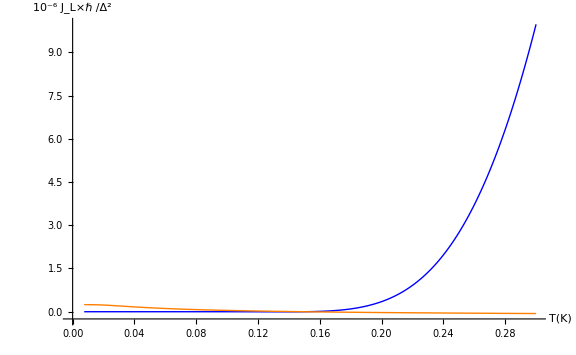

```mathematica
G1=PlotEngyFlowsWithTLTR[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,Full]
```

```mathematica
Export["image.pdf",G1,ImageResolution->300];
```

#### Forward and Reverse Energy Flows in Separate graphs

Forward Energy Flow

```mathematica
PlotEngyFlowsWithTLTRF[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=Jconv*10^6*Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
(*tempy2=10^19 Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];*)
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}](*,MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]*)}];
ListPlot[temp,AxesOrigin->{0,-0.25},AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["10^-6 J_L×ℏ /Δ^2",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{{Thickness->Large,Blue}(*,{Thickness->Large,Orange}*)},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],ImageSize->Large,Epilog->{Directive[{Gray,Dashed}],Line[{{0.15,-1},{0.15,9}}]}]]
```

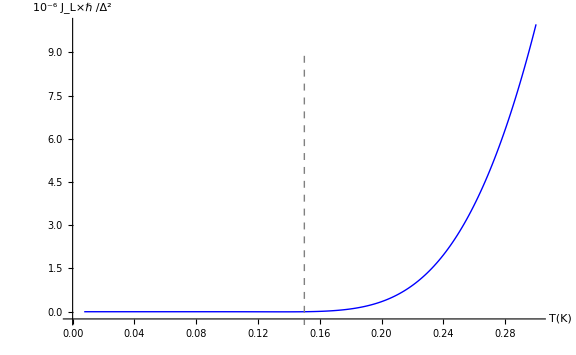

```mathematica
G1F=PlotEngyFlowsWithTLTRF[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,Full]
```

Reverse Energy Flow

```mathematica
PlotEngyFlowsWithTLTRR[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
(*tempy1=10^19 Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];*)
tempy2=Jconv*10^6*Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
temp=Table[{(*MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],*)MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,(*AxesOrigin->{0,-1},*)AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["10^-6 J_L×ℏ /Δ^2",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{(*{Thickness->Large,Blue},*){Thickness->Large,Orange}},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],Ticks->{If[Mod[#×10,0.05×10]==0,{#,Column[{#},ItemSize->{Automatic,1.5}],{.02,0}},{#,"",{.008,.0}}]&/@Range[0,0.3,0.01],If[Mod[#,2]==0,{#,Column[{#},ItemSize->{0.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-1,-0.5,0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}},ImageSize->Large,Epilog->{Directive[{Gray,Dashed}],Line[{{0.15,-3},{0.15,2}}]}]]
```

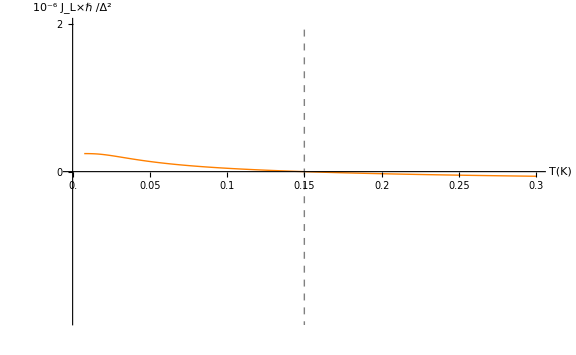

```mathematica
G1R=PlotEngyFlowsWithTLTRR[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,{{0,0.3},{-2,2}}]
```

#### Rectification Factor

```mathematica
PlotRecFacWithTL[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp,temp1,temp2},
tempy1=10^19 Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=10^19 Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
Size=Length[tempx];
temp=Table[MapThread[List,{tempx[[;;,1]],Abs[tempy1[[;;,1]]],Abs[tempy2[[;;,1]]]}]];
temp1=Table[Max[temp[[i,2]],temp[[i,3]]],{i,1,Size}];temp2=Table[MapThread[List,{tempx[[;;,1]],(Abs[(tempy1[[;;,1]]+tempy2[[;;,1]])])/temp1}]];
ListLogLinearPlot[temp2,AxesStyle->Directive[Darker[Gray],23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_L (K)",21.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["R(T_L,T_R=150mK)",21.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{Thickness->Large,Magenta},PlotRange->plotrange,Ticks->{Automatic,If[Mod[#×100,0.2×100]==0,{#,Column[{#},ItemSize->{1.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-0.1,-0.05,0.00,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.00,1.05,1.1}},ImageSize->700]]
```

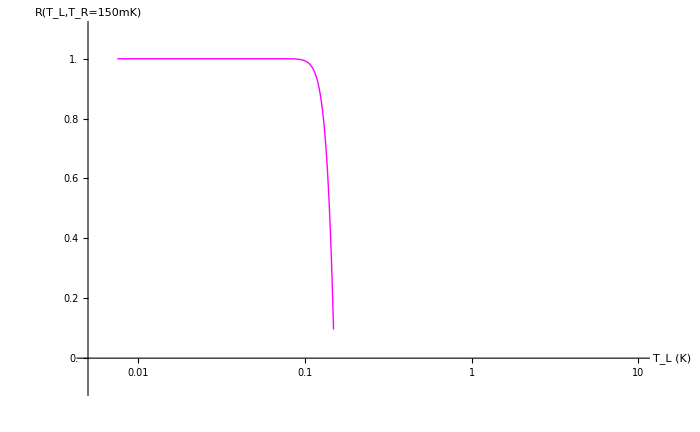

```mathematica
P1=PlotRecFacWithTL[0.005Tconv,0.1Tconv-0.001Tconv,0.001Tconv,0.1Tconv,0.95Econv,1Econv,0.05Econv,0.01Econv,{{0.005,10},{-0.1,1.1}}]
```

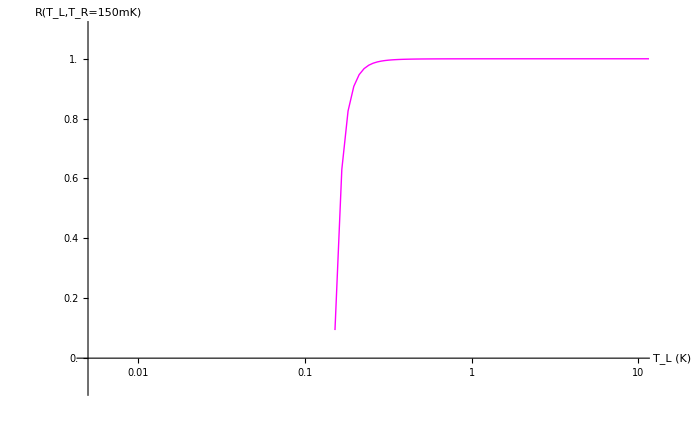

```mathematica
P2=PlotRecFacWithTL[0.1Tconv+0.001Tconv,10Tconv,0.01Tconv,0.1Tconv,0.95Econv,1Econv,0.05Econv,0.01Econv,{{0.005,10},{-0.1,1.1}}]
```

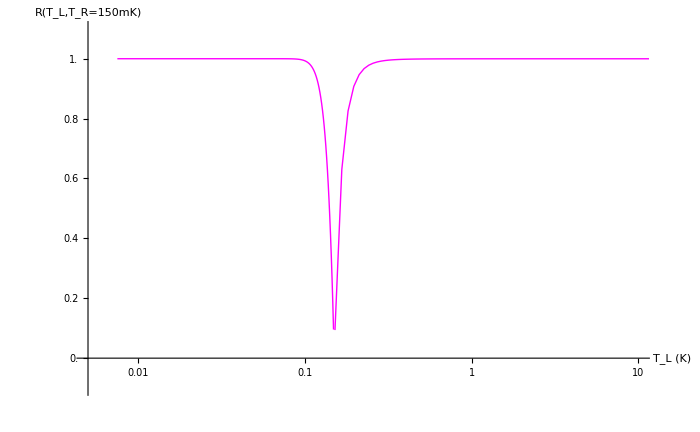

```mathematica
Show[P1,P2]
```

#### State and transition rate diagrams:

#### Forward Biased Diode

```mathematica
(*Subscript[Γ, L,1,3],Subscript[Γ, L,1,2],Subscript[Γ, L,2,4],Subscript[Γ, L,3,4],Subscript[Γ, L,3,5],Subscript[Γ, L,2,5],Subscript[Γ, L,4,6],Subscript[Γ, R,1,2],Subscript[Γ, R,1,3],Subscript[Γ, R,2,4],Subscript[Γ, R,3,4],Subscript[Γ, R,5,6]*)
```

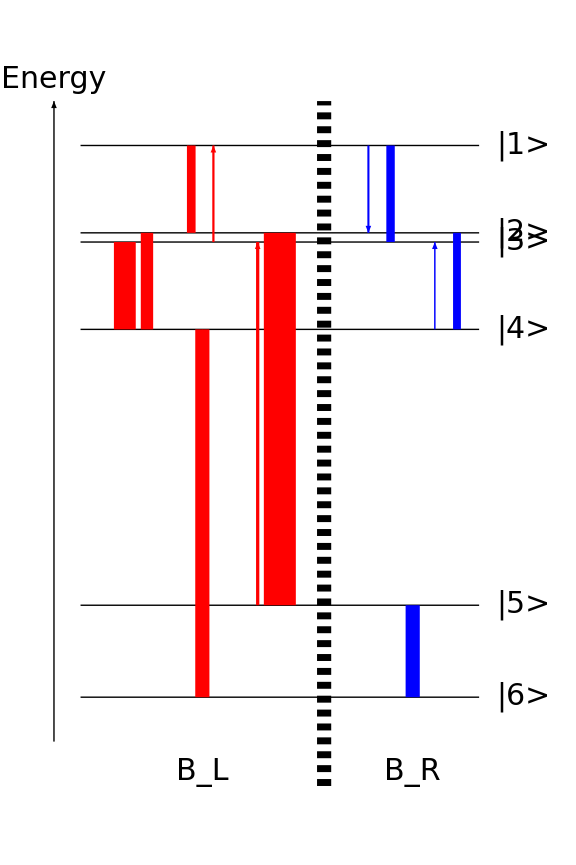

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.8Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.2 Econv,g->0.01Econv,κ-> 1 };
Evals={HsEVal}//.Flatten[{unitassum,TassumF}];
ypoints=Table[50×10^23×Evals[[1,1]][[y]],{y,1,6}];
States=Table[{"|1>","|2>","|3>","|4>","|5>","|6>"}];
SState=varFunc[0.2 Tconv,0.1 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum];
MaxRate=0.5*Max[SState[[2]]];
Graphics[{
Table[Line[{{15,50×10^23×Evals[[1,1]][[y]]},{105,ypoints[[y]]}}],{y,1,6}],
Table[Text[Style[States[[i]],30,FontFamily->"Times New Roman"],{115,50×10^23×Evals[[1,1]][[i]]}],{i,1,6}],Arrowheads[0.07],
Arrow[{{9,50×10^23×Evals[[1,1]][[6]]-10},{9,50×10^23×Evals[[1,1]][[1]]+10}}],
Text[Style["Energy",30,FontFamily->"Times New Roman"],{9,52×10^23×Evals[[1,1]][[1]]+10}],
Text[Style["B_L",30,FontFamily->"Times New Roman"],{42.5,50×10^23×Evals[[1,1]][[6]]-17}],Text[Style["B_R",30,FontFamily->"Times New Roman"],{90,50×10^23×Evals[[1,1]][[6]]-17}],
Red,Arrowheads[0.04],Thickness[0.02*Abs[SState[[2]][[1]]]/MaxRate],If[SState[[2]][[1]]>0,Arrow[{{45,ypoints[[1]]},{45,ypoints[[3]]}}],Arrow[{{45,ypoints[[3]]},{45,ypoints[[1]]}}]],
Red,Arrowheads[0.06],Thickness[0.02*Abs[SState[[2]][[2]]]/MaxRate],If[SState[[2]][[2]]>0,Arrow[{{40,ypoints[[1]]},{40,ypoints[[2]]}}],Arrow[{{40,ypoints[[2]]},{40,ypoints[[1]]}}]],
Red,Arrowheads[0.06],Thickness[0.02*Abs[SState[[2]][[3]]]/MaxRate],If[SState[[2]][[3]]>0,Arrow[{{30,ypoints[[2]]},{30,ypoints[[4]]}}],Arrow[{{30,ypoints[[4]]},{30,ypoints[[2]]}}]],
Red,Arrowheads[0.1],Thickness[0.02*Abs[SState[[2]][[4]]]/MaxRate],If[SState[[2]][[4]]>0,Arrow[{{25,ypoints[[3]]},{25,ypoints[[4]]}}],Arrow[{{25,ypoints[[4]]},{25,ypoints[[3]]}}]],
Red,Arrowheads[0.06],Thickness[0.02*Abs[SState[[2]][[5]]]/MaxRate],If[SState[[2]][[5]]>0,Arrow[{{55,ypoints[[3]]},{55,ypoints[[5]]}}],Arrow[{{55,ypoints[[5]]},{55,ypoints[[3]]}}]],
Red,Arrowheads[0.12],Thickness[0.02*Abs[SState[[2]][[6]]]/MaxRate],If[SState[[2]][[6]]>0,Arrow[{{60,ypoints[[2]]},{60,ypoints[[5]]}}],Arrow[{{60,ypoints[[5]]},{60,ypoints[[2]]}}]],
Red,Arrowheads[0.12],Thickness[0.02*Abs[SState[[2]][[7]]]/MaxRate],If[SState[[2]][[7]]>0,Arrow[{{42.5,ypoints[[4]]},{42.5,ypoints[[6]]}}],Arrow[{{42.5,ypoints[[6]]},{42.5,ypoints[[4]]}}]],
Blue,Arrowheads[0.05],Thickness[0.02*Abs[SState[[2]][[8]]]/MaxRate],If[SState[[2]][[8]]>0,Arrow[{{80,ypoints[[1]]},{80,ypoints[[2]]}}],Arrow[{{80,ypoints[[2]]},{80,ypoints[[1]]}}]],
Blue,Arrowheads[0.07],Thickness[0.02*Abs[SState[[2]][[9]]]/MaxRate],If[SState[[2]][[9]]>0,Arrow[{{85,ypoints[[1]]},{85,ypoints[[3]]}}],Arrow[{{85,ypoints[[3]]},{85,ypoints[[1]]}}]],
Blue,Arrowheads[0.06],Thickness[0.02*Abs[SState[[2]][[10]]]/MaxRate],If[SState[[2]][[10]]>0,Arrow[{{100,ypoints[[2]]},{100,ypoints[[4]]}}],Arrow[{{100,ypoints[[4]]},{100,ypoints[[2]]}}]],
Blue,Arrowheads[0.05],Thickness[0.02*Abs[SState[[2]][[11]]]/MaxRate],If[SState[[2]][[11]]>0,Arrow[{{95,ypoints[[3]]},{95,ypoints[[4]]}}],Arrow[{{95,ypoints[[4]]},{95,ypoints[[3]]}}]],
Blue,Arrowheads[0.1],Thickness[0.02*Abs[SState[[2]][[12]]]/MaxRate],If[SState[[2]][[12]]>0,Arrow[{{90,ypoints[[5]]},{90,ypoints[[6]]}}],Arrow[{{90,ypoints[[6]]},{90,ypoints[[5]]}}]],
Thickness[Tiny],Black,Dashed,Line[{{70,50×10^23×Evals[[1,1]][[6]]-20},{70,50×10^23×Evals[[1,1]][[1]]+10}}]
},ImageSize->Large]
```

#### Reverse Biased Diode

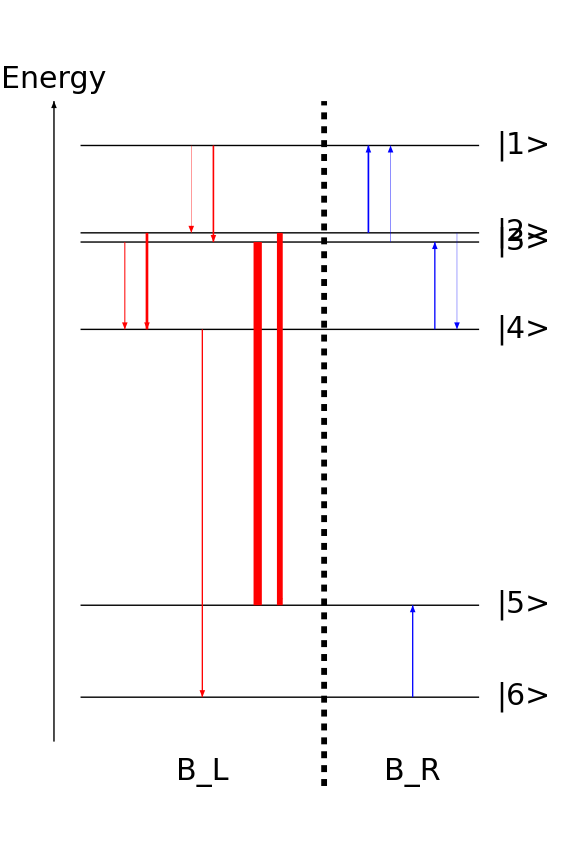

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.8Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.2 Econv,g->0.01Econv,κ-> 1 };
Evals={HsEVal}//.Flatten[{unitassum,TassumF}];
ypoints=Table[50×10^23×Evals[[1,1]][[y]],{y,1,6}];
States=Table[{"|1>","|2>","|3>","|4>","|5>","|6>"}];
SState=varFunc[0.1 Tconv,0.2 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum];
Graphics[{
Table[Line[{{15,50×10^23×Evals[[1,1]][[y]]},{105,ypoints[[y]]}}],{y,1,6}],
Table[Text[Style[States[[i]],30,FontFamily->"Times New Roman"],{115,50×10^23×Evals[[1,1]][[i]]}],{i,1,6}],Arrowheads[0.07],
Arrow[{{9,50×10^23×Evals[[1,1]][[6]]-10},{9,50×10^23×Evals[[1,1]][[1]]+10}}],
Text[Style["Energy",30,FontFamily->"Times New Roman"],{9,52×10^23×Evals[[1,1]][[1]]+10}],
Text[Style["B_L",30,FontFamily->"Times New Roman"],{42.5,50×10^23×Evals[[1,1]][[6]]-17}],Text[Style["B_R",30,FontFamily->"Times New Roman"],{90,50×10^23×Evals[[1,1]][[6]]-17}],
Red,Arrowheads[0.04],Thickness[0.4*Abs[SState[[2]][[1]]]/MaxRate],If[SState[[2]][[1]]>0,Arrow[{{45,ypoints[[1]]},{45,ypoints[[3]]}}],Arrow[{{45,ypoints[[3]]},{45,ypoints[[1]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[2]]]/MaxRate],If[SState[[2]][[2]]>0,Arrow[{{40,ypoints[[1]]},{40,ypoints[[2]]}}],Arrow[{{40,ypoints[[2]]},{40,ypoints[[1]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[3]]]/MaxRate],If[SState[[2]][[3]]>0,Arrow[{{30,ypoints[[2]]},{30,ypoints[[4]]}}],Arrow[{{30,ypoints[[4]]},{30,ypoints[[2]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[4]]]/MaxRate],If[SState[[2]][[4]]>0,Arrow[{{25,ypoints[[3]]},{25,ypoints[[4]]}}],Arrow[{{25,ypoints[[4]]},{25,ypoints[[3]]}}]],
Red,Arrowheads[0.06],Thickness[0.4*Abs[SState[[2]][[5]]]/MaxRate],If[SState[[2]][[5]]>0,Arrow[{{55,ypoints[[3]]},{55,ypoints[[5]]}}],Arrow[{{55,ypoints[[5]]},{55,ypoints[[3]]}}]],
Red,Arrowheads[0.04],Thickness[0.4*Abs[SState[[2]][[6]]]/MaxRate],If[SState[[2]][[6]]>0,Arrow[{{60,ypoints[[2]]},{60,ypoints[[5]]}}],Arrow[{{60,ypoints[[5]]},{60,ypoints[[2]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[7]]]/MaxRate],If[SState[[2]][[7]]>0,Arrow[{{42.5,ypoints[[4]]},{42.5,ypoints[[6]]}}],Arrow[{{42.5,ypoints[[6]]},{42.5,ypoints[[4]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[8]]]/MaxRate],If[SState[[2]][[8]]>0,Arrow[{{80,ypoints[[1]]},{80,ypoints[[2]]}}],Arrow[{{80,ypoints[[2]]},{80,ypoints[[1]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[9]]]/MaxRate],If[SState[[2]][[9]]>0,Arrow[{{85,ypoints[[1]]},{85,ypoints[[3]]}}],Arrow[{{85,ypoints[[3]]},{85,ypoints[[1]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[10]]]/MaxRate],If[SState[[2]][[10]]>0,Arrow[{{100,ypoints[[2]]},{100,ypoints[[4]]}}],Arrow[{{100,ypoints[[4]]},{100,ypoints[[2]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[11]]]/MaxRate],If[SState[[2]][[11]]>0,Arrow[{{95,ypoints[[3]]},{95,ypoints[[4]]}}],Arrow[{{95,ypoints[[4]]},{95,ypoints[[3]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[12]]]/MaxRate],If[SState[[2]][[12]]>0,Arrow[{{90,ypoints[[5]]},{90,ypoints[[6]]}}],Arrow[{{90,ypoints[[6]]},{90,ypoints[[5]]}}]],
Thickness[Tiny],Black,Dashed,Line[{{70,50×10^23×Evals[[1,1]][[6]]-20},{70,50×10^23×Evals[[1,1]][[1]]+10}}]
},ImageSize->Large]
```

# Qubit-Qubit Thermal Diode [26]

#### TLS Hamiltonian

```mathematica
H= ℏ/2*ω*Subscript[σ, z]
```

{{(ω ℏ)/2,0},{0,-(ω ℏ)/2}}

```mathematica
Eigenvalues[H]
```

{-(ω ℏ)/2,(ω ℏ)/2}

```mathematica
{SubMinus[z],SubPlus[z]}=Eigenvectors[H]
```

{{0,1},{1,0}}

#### 2nd Pauli Matrices (4 by 4) for system

```mathematica
Subscript[σ̃, z L]=KroneckerProduct[Subscript[σ, z],Subscript[σ, I]] ;
```

```mathematica
Subscript[σ̃, y L]=KroneckerProduct[Subscript[σ, y],Subscript[σ, I]] ;
```

```mathematica
Subscript[σ̃, x L]=KroneckerProduct[Subscript[σ, x],Subscript[σ, I]] ;
```

```mathematica
Subscript[σ̃, z R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, z]] ;
```

```mathematica
Subscript[σ̃, y R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, y]] ;
```

```mathematica
Subscript[σ̃, x R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, x]] ;
```

#### System Hamiltonian

```mathematica
Hs= ℏ/2*((Subscript[ω̃, L]*Subscript[σ̃, z L])+(Subscript[ω̃, R]*Subscript[σ̃, z R])+(Subscript[ω̃, RL]*Subscript[σ̃, z L]. Subscript[σ̃, z R]))
```

{{1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL),0,0,0},{0,1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL),0,0},{0,0,1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL),0},{0,0,0,1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL)}}

```mathematica
Eigensystem[Hs]
```

{{1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL),1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL),1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL),1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL)},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}}

```mathematica
OverTilde[HsEVal] ={1/2 ℏ (Subscript[ω̃, L]+Subscript[ω̃, R]+Subscript[ω̃, RL]),1/2 ℏ (Subscript[ω̃, L]-Subscript[ω̃, R]-Subscript[ω̃, RL]),1/2 ℏ (-Subscript[ω̃, L]+Subscript[ω̃, R]-Subscript[ω̃, RL]),1/2 ℏ (-Subscript[ω̃, L]-Subscript[ω̃, R]+Subscript[ω̃, RL])}//MatrixForm;
```

#### states of the system

```mathematica
SubPlus[z] SubPlus[z] = KroneckerProduct[SubPlus[z],SubPlus[z]]
```

Set::write: Tag Times in {1,0} {1,0} is Protected.

{{1,0},{0,0}}

```mathematica
SubPlus[z] SubMinus[z] = KroneckerProduct[SubPlus[z],SubMinus[z]]
```

Set::write: Tag Times in {0,1} {1,0} is Protected.

{{0,1},{0,0}}

```mathematica
SubMinus[z] SubMinus[z] = KroneckerProduct[SubMinus[z],SubMinus[z]]
```

Set::write: Tag Times in {0,1} {0,1} is Protected.

{{0,0},{0,1}}

```mathematica
SubMinus[z] SubPlus[z] = KroneckerProduct[SubMinus[z],SubPlus[z]]
```

Set::write: Tag Times in {0,1} {1,0} is Protected.

{{0,0},{1,0}}

```mathematica
Subscript[z, 1]= Transpose[{{1,0,0,0}}];
Subscript[z, 2]= Transpose[{{0,1,0,0}}];
Subscript[z, 3]= Transpose[{{0,0,1,0}}];
Subscript[z, 4]= Transpose[{{0,0,0,1}}];
```

#### Density Matrix

```mathematica
ρMatrix1[t]=Table[Subscript[ρ̃, i,j][t],{i,1,4},{j,1,4}];
MatrixForm[%]
```

((ρ̃)_(1,1)[t] | (ρ̃)_(1,2)[t] | (ρ̃)_(1,3)[t] | (ρ̃)_(1,4)[t]
(ρ̃)_(2,1)[t] | (ρ̃)_(2,2)[t] | (ρ̃)_(2,3)[t] | (ρ̃)_(2,4)[t]
(ρ̃)_(3,1)[t] | (ρ̃)_(3,2)[t] | (ρ̃)_(3,3)[t] | (ρ̃)_(3,4)[t]
(ρ̃)_(4,1)[t] | (ρ̃)_(4,2)[t] | (ρ̃)_(4,3)[t] | (ρ̃)_(4,4)[t])

#### Possible Transition Frequencies

```mathematica
ωMatrix1={Flatten[Table[Subscript[ω̃, j,i],{i,1,4},{j,i+1,4}]]}
```

{{(ω̃)_(2,1),(ω̃)_(3,1),(ω̃)_(4,1),(ω̃)_(3,2),(ω̃)_(4,2),(ω̃)_(4,3)}}

```mathematica
ωVals1=Flatten[Simplify[Table[-(OverTilde[HsEVal][[1,i]]-OverTilde[HsEVal][[1,j]]),{i,1,4},{j,i+1,4}]]]
```

{-ℏ ((ω̃)_R+(ω̃)_RL),-ℏ ((ω̃)_L+(ω̃)_RL),-ℏ ((ω̃)_L+(ω̃)_R),ℏ (-(ω̃)_L+(ω̃)_R),ℏ (-(ω̃)_L+(ω̃)_RL),ℏ (-(ω̃)_R+(ω̃)_RL)}

#### Allowed Transition Frequencies

```mathematica
ωMatrixA1={{Subscript[ω̃, 2,1],Subscript[ω̃, 4,1],Subscript[ω̃, 3,2],Subscript[ω̃, 4,3]}};
```

```mathematica
ωValsA1={{-ℏ (Subscript[ω̃, R]+Subscript[ω̃, RL]),-ℏ (Subscript[ω̃, L]+Subscript[ω̃, R]),ℏ (-Subscript[ω̃, L]+Subscript[ω̃, R]),ℏ (-Subscript[ω̃, R]+Subscript[ω̃, RL])}};
```

#### Projection Operators

```mathematica
Subscript[πMatrix1, i_] := Subscript[z, i].Subscript[z, i] ᵀ
```

#### Lindblad Operator

```mathematica
Subscript[AMatrix1, P_,Subscript[ω̃, j_,i_]]:= Subscript[πMatrix1, i].Subscript[σ̃, x P].Subscript[πMatrix1, j]
```

```mathematica
Subscript[σ̃, x L]
```

{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}

```mathematica
Subscript[σ̃, x R]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

#### Lindblad Super Operator

```mathematica
Subscript[ℒ̃, P_]:=Subscript[ℒ̃, P]=∑_(α=1)^6 (Subscript[𝒥̃, P][Part[ωMatrix1,1,α]](1+Subscript[n, P][Part[ωMatrix1,1,α]])(Subscript[AMatrix1, P,Part[ωMatrix1,1,α]].ρMatrix1[t].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ-1/2 Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ.Subscript[AMatrix1, P,Part[ωMatrix1,1,α]].ρMatrix1[t]-1/2 ρMatrix1[t].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ.Subscript[AMatrix1, P,Part[ωMatrix1,1,α]])+(Subscript[𝒥̃, P][Part[ωMatrix1,1,α]] Subscript[n, P][Part[ωMatrix1,1,α]](Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ.ρMatrix1[t].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]]-1/2 Subscript[AMatrix1, P,Part[ωMatrix1,1,α]].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ.ρMatrix1[t]-1/2 ρMatrix1[t].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]].Subscript[AMatrix1, P,Part[ωMatrix1,1,α]] ᵀ)))/.{-Subscript[ρ̃, i_,i_][t] Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]]Subscript[n, Q_][Subscript[ω̃, j_,i_]]+Subscript[ρ̃, j_,j_][t]Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]](1+Subscript[n, Q_][Subscript[ω̃, j_,i_]]):>Subscript[Γ̃, Q,j,i],Subscript[ρ̃, i_,i_][t] Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]]Subscript[n, Q_][Subscript[ω̃, j_,i_]]-Subscript[ρ̃, j_,j_][t]Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]](1+Subscript[n, Q_][Subscript[ω̃, j_,i_]]):>-Subscript[Γ̃, Q,j,i]};
```

#### Master Equation

```mathematica
dρ1=MatrixForm[Simplify[Subscript[ℒ̃, L]+Subscript[ℒ̃, R]-(ⅈ/ℏ(Hs.ρMatrix1[t]-ρMatrix1[t].Hs))]]
```

((Γ̃)_(L,3,1)+(Γ̃)_(R,2,1) | -1/2 ⅈ (2 (ω̃)_R+2 (ω̃)_RL-ⅈ (n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)]+n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)]+(1+2 n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)])) (ρ̃)_(1,2)[t] | -1/2 ⅈ (2 (ω̃)_L+2 (ω̃)_RL-ⅈ ((1+2 n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(1,3)[t] | -1/2 ⅈ (2 (ω̃)_L+2 (ω̃)_R-ⅈ (n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)]+(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+(𝒥̃)_R[(ω̃)_(4,3)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(1,4)[t]
1/2 ⅈ (2 (ω̃)_R+2 (ω̃)_RL+ⅈ (n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)]+n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)]+(1+2 n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)])) (ρ̃)_(2,1)[t] | (Γ̃)_(L,4,2)-(Γ̃)_(R,2,1) | -1/2 ⅈ (2 (ω̃)_L-2 (ω̃)_R-ⅈ ((1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)]+(𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(2,3)[t] | -1/2 ⅈ (2 (ω̃)_L-2 (ω̃)_RL-ⅈ ((1+2 n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+(1+n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)]+(1+n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(2,4)[t]
1/2 ⅈ (2 (ω̃)_L+2 (ω̃)_RL+ⅈ ((1+2 n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(3,1)[t] | 1/2 ⅈ (2 (ω̃)_L-2 (ω̃)_R+ⅈ ((1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)]+(𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(3,2)[t] | -(Γ̃)_(L,3,1)+(Γ̃)_(R,4,3) | -1/2 ⅈ (2 (ω̃)_R-2 (ω̃)_RL-ⅈ ((1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+(1+2 n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(3,4)[t]
1/2 ⅈ (2 (ω̃)_L+2 (ω̃)_R+ⅈ (n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)]+(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)]+(𝒥̃)_R[(ω̃)_(4,3)]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(4,1)[t] | 1/2 ⅈ (2 (ω̃)_L-2 (ω̃)_RL+ⅈ ((1+2 n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+(1+n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)]+(1+n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(4,2)[t] | 1/2 ⅈ (2 (ω̃)_R-2 (ω̃)_RL+ⅈ ((1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)]+(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)]+(1+2 n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)])) (ρ̃)_(4,3)[t] | -(Γ̃)_(L,4,2)-(Γ̃)_(R,4,3))

#### Thermal Energy Flows

```mathematica
HsMatrix1=DiagonalMatrix[ℏ{Subscript[ω̃, 1],Subscript[ω̃, 2],Subscript[ω̃, 3],Subscript[ω̃, 4]}]
```

{{ℏ (ω̃)_1,0,0,0},{0,ℏ (ω̃)_2,0,0},{0,0,ℏ (ω̃)_3,0},{0,0,0,ℏ (ω̃)_4}}

```mathematica
Subscript[J̃, P_]:=Subscript[J̃, P]=Simplify[Tr[HsMatrix1.Subscript[ℒ̃, P]]]/.{-Subscript[ρ̃, i_,i_][t] Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]]Subscript[n, Q_][Subscript[ω̃, j_,i_]]+Subscript[ρ̃, j_,j_][t]Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]](1+Subscript[n, Q_][Subscript[ω̃, j_,i_]]):>Subscript[Γ̃, Q,j,i],Subscript[ρ̃, i_,i_][t] Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]]Subscript[n, Q_][Subscript[ω̃, j_,i_]]-Subscript[ρ̃, j_,j_][t]Subscript[𝒥̃, Q_][Subscript[ω̃, j_,i_]](1+Subscript[n, Q_][Subscript[ω̃, j_,i_]]):>-Subscript[Γ̃, P,j,i]};
```

```mathematica
Subscript[J̃, L]
Subscript[J̃, R]
```

ℏ ((ω̃)_1 (Γ̃)_(L,3,1)-(ω̃)_3 (Γ̃)_(L,3,1)+((ω̃)_2-(ω̃)_4) (Γ̃)_(L,4,2))

ℏ ((ω̃)_1 (Γ̃)_(R,2,1)-(ω̃)_2 (Γ̃)_(R,2,1)+((ω̃)_3-(ω̃)_4) (Γ̃)_(R,4,3))

### Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum1=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T̃, P]))-1);
```

#### Stationary State Solutions of master equation

```mathematica
OverTilde[RHS]=Subscript[ℒ̃, L]+Subscript[ℒ̃, R]-(ⅈ/ℏ(Hs.ρMatrix1[t]-ρMatrix1[t].Hs))/.{Subscript[Γ̃, P_,j_,i_]->-Subscript[ρ̃, i,i][t] Subscript[𝒥̃, P][Subscript[ω̃, j,i]]Subscript[n, P][Subscript[ω̃, j,i]]+Subscript[ρ̃, j,j][t]Subscript[𝒥̃, P][Subscript[ω̃, j,i]](1+Subscript[n, P][Subscript[ω̃, j,i]]),Subscript[𝒥̃, P_][Subscript[ω̃, j_,i_]]->𝒥̃[Subscript[ω̃, j,i]]};
```

```mathematica
MatrixForm[%]
```

(-n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)] (ρ̃)_(1,1)[t]-n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)] (ρ̃)_(1,1)[t]+(1+n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)] (ρ̃)_(2,2)[t]+(1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)] (ρ̃)_(3,3)[t] | -1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(1,2)[t]-1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(1,2)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(1,2)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(1,2)[t]-(ⅈ (-1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(1,2)[t]+1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(1,2)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(1,3)[t]-1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(1,3)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(1,3)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(1,3)[t]-(ⅈ (-1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(1,3)[t]+1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(1,3)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(1,4)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(1,4)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(1,4)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(1,4)[t]-(ⅈ (-1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(1,4)[t]+1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(1,4)[t]))/ℏ
-1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(2,1)[t]-1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(2,1)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(2,1)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(2,1)[t]-(ⅈ (1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(2,1)[t]-1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(2,1)[t]))/ℏ | n_R[(ω̃)_(2,1)] (𝒥̃)_R[(ω̃)_(2,1)] (ρ̃)_(1,1)[t]-n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)] (ρ̃)_(2,2)[t]-(1+n_R[(ω̃)_(2,1)]) (𝒥̃)_R[(ω̃)_(2,1)] (ρ̃)_(2,2)[t]+(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)] (ρ̃)_(4,4)[t] | -1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(2,3)[t]-1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(2,3)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(2,3)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(2,3)[t]-(ⅈ (1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(2,3)[t]-1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(2,3)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(2,4)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(2,4)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(2,4)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(2,4)[t]-(ⅈ (1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(2,4)[t]-1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(2,4)[t]))/ℏ
-1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(3,1)[t]-1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(3,1)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(3,1)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(3,1)[t]-(ⅈ (1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(3,1)[t]-1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(3,1)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(3,2)[t]-1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(3,2)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(3,2)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(3,2)[t]-(ⅈ (-1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(3,2)[t]+1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(3,2)[t]))/ℏ | n_L[(ω̃)_(3,1)] (𝒥̃)_L[(ω̃)_(3,1)] (ρ̃)_(1,1)[t]-(1+n_L[(ω̃)_(3,1)]) (𝒥̃)_L[(ω̃)_(3,1)] (ρ̃)_(3,3)[t]-n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)] (ρ̃)_(3,3)[t]+(1+n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)] (ρ̃)_(4,4)[t] | -1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(3,4)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(3,4)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(3,4)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(3,4)[t]-(ⅈ (1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(3,4)[t]-1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(3,4)[t]))/ℏ
-1/2 𝒥̃[(ω̃)_(3,1)] n_L[(ω̃)_(3,1)] (ρ̃)_(4,1)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(4,1)[t]-1/2 𝒥̃[(ω̃)_(2,1)] n_R[(ω̃)_(2,1)] (ρ̃)_(4,1)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(4,1)[t]-(ⅈ (1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(4,1)[t]-1/2 ℏ ((ω̃)_L+(ω̃)_R+(ω̃)_RL) (ρ̃)_(4,1)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(4,2)] n_L[(ω̃)_(4,2)] (ρ̃)_(4,2)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(4,2)[t]-1/2 𝒥̃[(ω̃)_(2,1)] (1+n_R[(ω̃)_(2,1)]) (ρ̃)_(4,2)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(4,2)[t]-(ⅈ (-1/2 ℏ ((ω̃)_L-(ω̃)_R-(ω̃)_RL) (ρ̃)_(4,2)[t]+1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(4,2)[t]))/ℏ | -1/2 𝒥̃[(ω̃)_(3,1)] (1+n_L[(ω̃)_(3,1)]) (ρ̃)_(4,3)[t]-1/2 𝒥̃[(ω̃)_(4,2)] (1+n_L[(ω̃)_(4,2)]) (ρ̃)_(4,3)[t]-1/2 𝒥̃[(ω̃)_(4,3)] n_R[(ω̃)_(4,3)] (ρ̃)_(4,3)[t]-1/2 𝒥̃[(ω̃)_(4,3)] (1+n_R[(ω̃)_(4,3)]) (ρ̃)_(4,3)[t]-(ⅈ (-1/2 ℏ (-(ω̃)_L+(ω̃)_R-(ω̃)_RL) (ρ̃)_(4,3)[t]+1/2 ℏ (-(ω̃)_L-(ω̃)_R+(ω̃)_RL) (ρ̃)_(4,3)[t]))/ℏ | n_L[(ω̃)_(4,2)] (𝒥̃)_L[(ω̃)_(4,2)] (ρ̃)_(2,2)[t]+n_R[(ω̃)_(4,3)] (𝒥̃)_R[(ω̃)_(4,3)] (ρ̃)_(3,3)[t]-(1+n_L[(ω̃)_(4,2)]) (𝒥̃)_L[(ω̃)_(4,2)] (ρ̃)_(4,4)[t]-(1+n_R[(ω̃)_(4,3)]) (𝒥̃)_R[(ω̃)_(4,3)] (ρ̃)_(4,4)[t])

```mathematica
OverTilde[LHS]=D[ρMatrix1[t], t];
MatrixForm[%]
```

((ρ̃)_(1,1)'[t] | (ρ̃)_(1,2)'[t] | (ρ̃)_(1,3)'[t] | (ρ̃)_(1,4)'[t]
(ρ̃)_(2,1)'[t] | (ρ̃)_(2,2)'[t] | (ρ̃)_(2,3)'[t] | (ρ̃)_(2,4)'[t]
(ρ̃)_(3,1)'[t] | (ρ̃)_(3,2)'[t] | (ρ̃)_(3,3)'[t] | (ρ̃)_(3,4)'[t]
(ρ̃)_(4,1)'[t] | (ρ̃)_(4,2)'[t] | (ρ̃)_(4,3)'[t] | (ρ̃)_(4,4)'[t])

```mathematica
OverTilde[sol]=Flatten[Solve[OverTilde[LHS]==OverTilde[RHS],Flatten[Table[Subscript[ρ̃, i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
OverTilde[soldiag]=OverTilde[sol][[1;; ;;5]];
OverTilde[soloffdiag]=Delete[OverTilde[sol],Table[{1+5i},{i,0,3}]];
```

Off diagonal Solutions

```mathematica
Flatten[{OverTilde[soloffdiag]/.{Subscript[ρ̃, i_,j_]'[t]-> 0,Subscript[ρ̃, i_,j_][t]-> Subscript[ρ̃, i,j]}}];
OverTilde[soloffdiagstat]=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ̃, i,j]-i,j Subscript[ρ̃, i,j],{i,1,4},{j,1,4}]],0]]
```

{{(ρ̃)_(1,2)→0,(ρ̃)_(1,3)→0,(ρ̃)_(1,4)→0,(ρ̃)_(2,1)→0,(ρ̃)_(2,3)→0,(ρ̃)_(2,4)→0,(ρ̃)_(3,1)→0,(ρ̃)_(3,2)→0,(ρ̃)_(3,4)→0,(ρ̃)_(4,1)→0,(ρ̃)_(4,2)→0,(ρ̃)_(4,3)→0}}

```mathematica
Flatten[{OverTilde[soloffdiag]/.Subscript[ρ̃, i_,j_][t]-> i,j Subscript[ρ̃, i,j]}]
```

{(ρ̃)_(1,2)'[t]==0,(ρ̃)_(1,3)'[t]==0,(ρ̃)_(1,4)'[t]==0,(ρ̃)_(2,1)'[t]==0,(ρ̃)_(2,3)'[t]==0,(ρ̃)_(2,4)'[t]==0,(ρ̃)_(3,1)'[t]==0,(ρ̃)_(3,2)'[t]==0,(ρ̃)_(3,4)'[t]==0,(ρ̃)_(4,1)'[t]==0,(ρ̃)_(4,2)'[t]==0,(ρ̃)_(4,3)'[t]==0}

Assumptions for the calculations

```mathematica
ωassum3=Flatten[{Table[Subscript[ω̃, i,j]->(OverTilde[HsEVal][[1,i]]-OverTilde[HsEVal][[1,j]] )/ℏ,{i,1,4},{j,1,4}]}];
ωassum4={Table[Subscript[ω̃, i]-> OverTilde[HsEVal][[1,i]]/ℏ,{i,1,4}]};
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τimeconv=(Tconv k)/ℏ/.unitassum;
Jconv=ℏ/Econv^2 /.unitassum;
Jassum2=Subscript[𝒥̃, p_][ω_]->κ ω;
Jassum3=𝒥̃[ω_]->κ ω;
TassumF1={Subscript[T̃, L]-> 0.2 Tconv,Subscript[T̃, R]-> 0.02 Tconv,Subscript[ω̃, L]->1 ωconv,Subscript[ω̃, R]->0 ωconv,Subscript[ω̃, RL]->0.1ωconv,κ-> 1 };
TassumR1={Subscript[T̃, L]-> 0.02 Tconv,Subscript[T̃, R]-> 0.2 Tconv,Subscript[ω̃, L]->1 ωconv,Subscript[ω̃, R]->0 ωconv,Subscript[ω̃, RL]->0.1ωconv,κ-> 1 };
tmax=(2100/(10*ωconv));
```

```mathematica
OverTilde[dynamicsF]=NDSolve[Flatten[{OverTilde[sol]//.Flatten[{Jassum2,Jassum3,NBEassum1,TassumF1,unitassum,ωassum3}],Table[Subscript[ρ̃, i,j][0]==i,j i,1 1,{i,1,4},{j,1,4}]}],Flatten[Table[Subscript[ρ̃, i,j],{i,1,4},{j,1,4}]],{t,0,10*tmax}];
OverTilde[dynamicsR]=NDSolve[Flatten[{OverTilde[sol]//.Flatten[{Jassum2,Jassum3,NBEassum1,TassumR1,unitassum,ωassum3}],Table[Subscript[ρ̃, i,j][0]==i,j i,1 1,{i,1,4},{j,1,4}]}],Flatten[Table[Subscript[ρ̃, i,j],{i,1,4},{j,1,4}]],{t,0,10*tmax}];
```

#### Density Matrix Element Plots

Forward Condition

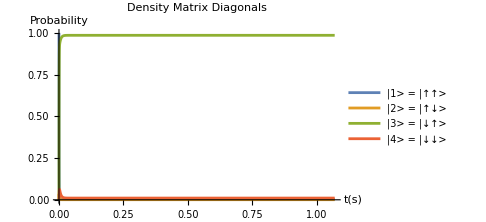

```mathematica
Flatten[{Table[Subscript[ρ̃, i,i][t],{i,1,4}]}/. OverTilde[dynamicsF]];
Plot[%,{t,0,10*tmax},PlotRange-> Automatic,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1> = |↑↑> "],
Style["|2> = |↑↓> "],
Style["|3> = |↓↑> "],
Style["|4> = |↓↓> "]},ImageSize->Medium]
```

Reverse Condition

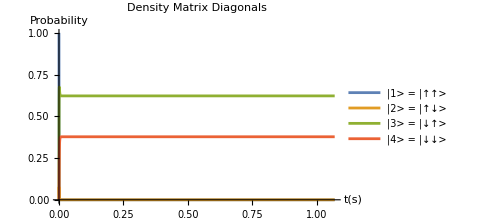

```mathematica
Flatten[{Table[Subscript[ρ̃, i,i][t],{i,1,4}]}/. OverTilde[dynamicsR]];
Plot[%,{t,0,10*tmax},PlotRange-> Automatic,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1> = |↑↑> "],
Style["|2> = |↑↓> "],
Style["|3> = |↓↑> "],
Style["|4> = |↓↓> "]},ImageSize->Medium]
```

#### Transition Rates

```mathematica
Subscript[Γ̃, P_,j_,i_]=-Subscript[ρ̃, i,i][t] Subscript[𝒥̃, P][Subscript[ω̃, j,i]]Subscript[n, P][Subscript[ω̃, j,i]]+Subscript[ρ̃, j,j][t]Subscript[𝒥̃, P][Subscript[ω̃, j,i]](1+Subscript[n, P][Subscript[ω̃, j,i]]);
```

#### Steady State Solutions for density matrices, transition rates and energy flows

```mathematica
varFunc1[TL_,TR_,ωLs_,ωRs_,ωRLs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum2,Jassum3,ωassum3,ωassum4,NBEassum1,unitassum,κ-> 1,Subscript[T̃, L]-> TL,Subscript[T̃, R]-> TR,Subscript[ω̃, L]->ωLs,Subscript[ω̃, R]->ωRs,Subscript[ω̃, RL]->ωRLs}];
temp1=N[OverTilde[sol]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̃, i_,j_]'[t]-> 0,Subscript[ρ̃, i_,j_][t]-> Subscript[ρ̃, i,j]},1==∑_(i=1)^4 Subscript[ρ̃, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̃, i,j],{i,1,4},{j,1,4}]]]]];
Re[{Flatten[Table[Subscript[ρ̃, i,i],{i,1,4}]/.temp3],Flatten[{Subscript[Γ̃, L,3,1],Subscript[Γ̃, L,2,4],Subscript[Γ̃, R,1,2],Subscript[Γ̃, R,4,3]}//.Flatten[{Subscript[ρ̃, i_,j_][t]->Subscript[ρ̃, i,j],temp0}]/.temp3],Flatten[{Subscript[J̃, L],Subscript[J̃, R]}//.Flatten[{Subscript[ρ̃, i_,j_][t]->Subscript[ρ̃, i,j],temp0}]/.temp3]}]]
```

```mathematica
varFunc1[0.2 Tconv,0.1 Tconv,1 ωconv,0.05 ωconv,0.01 ωconv,unitassum]
varFunc1[0.1Tconv,0.2 Tconv,1 ωconv,0.05 ωconv,0.01 ωconv,unitassum]
```

{{0.00252763,0.00423976,0.398465,0.594768},{5.24341×10^6,5.24341×10^6,5.24341×10^6,5.24341×10^6},{2.17172×10^-18,-2.17172×10^-18}}

{{0.0000188096,0.0000272622,0.450146,0.549808},{-63037.8,-63037.8,-63037.8,-63037.8},{-2.6109×10^-20,2.6109×10^-20}}

#### Plots for adjusting T_L and T_R (at steady state):

#### Energy Inflows

```mathematica
varEngyFunc1[TL_,TR_,ωLs_,ωRs_,ωRLs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum2,Jassum3,ωassum3,ωassum4,NBEassum1,unitassum,κ-> 1,Subscript[T̃, L]-> TL,Subscript[T̃, R]-> TR,Subscript[ω̃, L]->ωLs,Subscript[ω̃, R]->ωRs,Subscript[ω̃, RL]->ωRLs}];
temp1=N[OverTilde[sol]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̃, i_,j_]'[t]-> 0,Subscript[ρ̃, i_,j_][t]-> Subscript[ρ̃, i,j]},1==∑_(i=1)^4 Subscript[ρ̃, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̃, i,j],{i,1,4},{j,1,4}]]]]];
Re[Flatten[{Subscript[J̃, L]}//.Flatten[{Subscript[ρ̃, i_,j_][t]->Subscript[ρ̃, i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTLTR1[Tmin_,Tmax_,Tres_,Tfix_,ωLs_,ωRs_,ωRLs_,plotrange_,plotlegend_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempy1=Jconv*10^7*Table[varEngyFunc1[TL,Tfix,ωLs,ωRs,ωRLs,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=Jconv*10^7*Table[varEngyFunc1[Tfix,TR,ωLs,ωRs,ωRLs,unitassum],{TR,Tmin,Tmax,Tres}];
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,AxesStyle->Directive[Darker[Gray],26.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",26.5,FontFamily->"Times New Roman"],Style["10^-7 J_L×ℏ /Δ^2",26.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{{Dashed,Blue},{Dashed,Orange}}(*,PlotLegends->Placed[plotlegend,Below]*),PlotRange->plotrange,ImageSize->Large]]
```

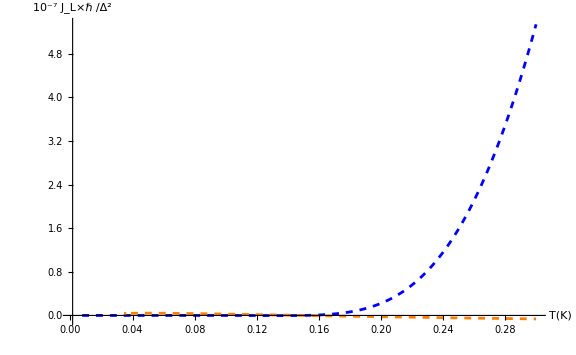

```mathematica
G3=PlotEngyFlowsWithTLTR1[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,1ωconv,0.05ωconv,0.01ωconv,Full,{Style["J_L(T_L=T, T_R=150mK)",26.5,FontFamily->"Times New Roman"],Style["J_L(T_L=150mK, T_R=T)",26.5,FontFamily->"Times New Roman"]}]
```

# Comparing two models

#### Thermal flow comparison-both together

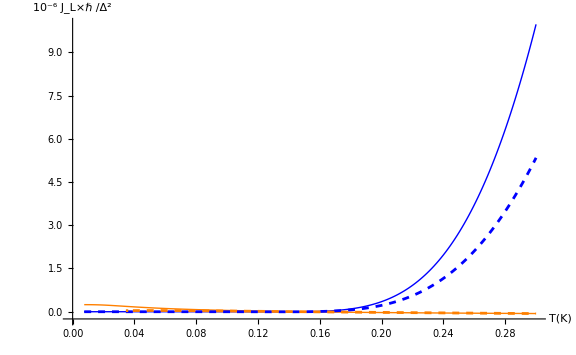

```mathematica
Show[G1,PlotEngyFlowsWithTLTR1[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,1ωconv,0.05ωconv,0.01ωconv,Full,{Style["(J̄)_L(T_L=T, T_R=150mK)",26.5,FontFamily->"Times New Roman"],Style["(J̄)_L(T_L=150mK, T_R=T)",26.5,FontFamily->"Times New Roman"]}]]
```